```mathematica
ClearAll["Global`*"]
```

```mathematica
Dummy=Array[0&,{12,12}];
Dummy//MatrixForm
```

```mathematica
H=({{0, b1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {b1/2, -AC, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, b1/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, b1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, b1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, b1/2, -AN-AC, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, b1/2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, b1/2, -AN, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, b1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, b1/2, -2*AN-AC, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b1/2}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b1/2, -2*AN}});
H//MatrixForm
```

```mathematica
H0=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -AC, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -AN-AC, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, -AN, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -2*AN-AC, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -2*AN}});
```

```mathematica
U=MatrixExp[-ⅈ*t*H]//FullSimplify;
U//MatrixForm
U0=MatrixExp[-ⅈ*t*H0]/.t->-π/b1//FullSimplify;
U0//MatrixForm
```

(ⅇ^((ⅈ AC t)/2) (Cos[1/2 √(AC^2+b1^2) t]-(ⅈ AC Sin[1/2 √(AC^2+b1^2) t])/(√(AC^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AC t)/2) Sin[1/2 √(AC^2+b1^2) t])/(√(AC^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(ⅈ b1 ⅇ^((ⅈ AC t)/2) Sin[1/2 √(AC^2+b1^2) t])/(√(AC^2+b1^2)) | ⅇ^((ⅈ AC t)/2) (Cos[1/2 √(AC^2+b1^2) t]+(ⅈ AC Sin[1/2 √(AC^2+b1^2) t])/(√(AC^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Cos[(b1 t)/2] | -ⅈ Sin[(b1 t)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ Sin[(b1 t)/2] | Cos[(b1 t)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(1/2 ⅈ (AC+AN) t) (Cos[1/2 √((AC+AN)^2+b1^2) t]-(ⅈ (AC+AN) Sin[1/2 √((AC+AN)^2+b1^2) t])/(√((AC+AN)^2+b1^2))) | -(ⅈ b1 ⅇ^(1/2 ⅈ (AC+AN) t) Sin[1/2 √((AC+AN)^2+b1^2) t])/(√((AC+AN)^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^(1/2 ⅈ (AC+AN) t) Sin[1/2 √((AC+AN)^2+b1^2) t])/(√((AC+AN)^2+b1^2)) | ⅇ^(1/2 ⅈ (AC+AN) t) (Cos[1/2 √((AC+AN)^2+b1^2) t]+(ⅈ (AC+AN) Sin[1/2 √((AC+AN)^2+b1^2) t])/(√((AC+AN)^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ AN t)/2) (Cos[1/2 √(AN^2+b1^2) t]-(ⅈ AN Sin[1/2 √(AN^2+b1^2) t])/(√(AN^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AN t)/2) Sin[1/2 √(AN^2+b1^2) t])/(√(AN^2+b1^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^((ⅈ AN t)/2) Sin[1/2 √(AN^2+b1^2) t])/(√(AN^2+b1^2)) | ⅇ^((ⅈ AN t)/2) (Cos[1/2 √(AN^2+b1^2) t]+(ⅈ AN Sin[1/2 √(AN^2+b1^2) t])/(√(AN^2+b1^2))) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(1/2 ⅈ (AC+2 AN) t) (Cos[1/2 √((AC+2 AN)^2+b1^2) t]-(ⅈ (AC+2 AN) Sin[1/2 √((AC+2 AN)^2+b1^2) t])/(√((AC+2 AN)^2+b1^2))) | -(ⅈ b1 ⅇ^(1/2 ⅈ (AC+2 AN) t) Sin[1/2 √((AC+2 AN)^2+b1^2) t])/(√((AC+2 AN)^2+b1^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^(1/2 ⅈ (AC+2 AN) t) Sin[1/2 √((AC+2 AN)^2+b1^2) t])/(√((AC+2 AN)^2+b1^2)) | ⅇ^(1/2 ⅈ (AC+2 AN) t) (Cos[1/2 √((AC+2 AN)^2+b1^2) t]+(ⅈ (AC+2 AN) Sin[1/2 √((AC+2 AN)^2+b1^2) t])/(√((AC+2 AN)^2+b1^2))) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ AN t) (Cos[1/2 √(4 AN^2+b1^2) t]-(2 ⅈ AN Sin[1/2 √(4 AN^2+b1^2) t])/(√(4 AN^2+b1^2))) | -(ⅈ b1 ⅇ^(ⅈ AN t) Sin[1/2 √(4 AN^2+b1^2) t])/(√(4 AN^2+b1^2))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^(ⅈ AN t) Sin[1/2 √(4 AN^2+b1^2) t])/(√(4 AN^2+b1^2)) | ⅇ^(ⅈ AN t) (Cos[1/2 √(4 AN^2+b1^2) t]+(2 ⅈ AN Sin[1/2 √(4 AN^2+b1^2) t])/(√(4 AN^2+b1^2))))

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(-(ⅈ AC π)/b1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(-(ⅈ (AC+AN) π)/b1) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-(ⅈ AN π)/b1) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-(ⅈ (AC+2 AN) π)/b1) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-(2 ⅈ AN π)/b1))

```mathematica
Uc1=U/.t->n*π/b1//FullSimplify;
Uc1//MatrixForm
```

(ⅇ^((ⅈ AC n π)/(2 b1)) (Cos[(√(AC^2+b1^2) n π)/(2 b1)]-(ⅈ AC Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AC n π)/(2 b1)) Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(ⅈ b1 ⅇ^((ⅈ AC n π)/(2 b1)) Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2)) | ⅇ^((ⅈ AC n π)/(2 b1)) (Cos[(√(AC^2+b1^2) n π)/(2 b1)]+(ⅈ AC Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Cos[(n π)/2] | -ⅈ Sin[(n π)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ Sin[(n π)/2] | Cos[(n π)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^((ⅈ (AC+AN) n π)/(2 b1)) (Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)]-(ⅈ (AC+AN) Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ (AC+AN) n π)/(2 b1)) Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^((ⅈ (AC+AN) n π)/(2 b1)) Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2)) | ⅇ^((ⅈ (AC+AN) n π)/(2 b1)) (Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)]+(ⅈ (AC+AN) Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ AN n π)/(2 b1)) (Cos[(√(AN^2+b1^2) n π)/(2 b1)]-(ⅈ AN Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AN n π)/(2 b1)) Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^((ⅈ AN n π)/(2 b1)) Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2)) | ⅇ^((ⅈ AN n π)/(2 b1)) (Cos[(√(AN^2+b1^2) n π)/(2 b1)]+(ⅈ AN Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2))) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ (AC+2 AN) n π)/(2 b1)) (Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)]-(ⅈ (AC+2 AN) Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ (AC+2 AN) n π)/(2 b1)) Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^((ⅈ (AC+2 AN) n π)/(2 b1)) Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2)) | ⅇ^((ⅈ (AC+2 AN) n π)/(2 b1)) (Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)]+(ⅈ (AC+2 AN) Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2))) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ AN n π)/b1) (Cos[(√(4 AN^2+b1^2) n π)/(2 b1)]-(2 ⅈ AN Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AN n π)/b1) Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^((ⅈ AN n π)/b1) Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2)) | ⅇ^((ⅈ AN n π)/b1) (Cos[(√(4 AN^2+b1^2) n π)/(2 b1)]+(2 ⅈ AN Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2))))

```mathematica
Transpose[Conjugate[Uc1]].Uc1//ComplexExpand//Simplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Rz1=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ((-1)^n)*-ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ((-1)^n)*-ⅈ, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
Uc2=Rz1.Uc1;
Uc2//MatrixForm
```

(ⅇ^((ⅈ AC n π)/(2 b1)) (Cos[(√(AC^2+b1^2) n π)/(2 b1)]-(ⅈ AC Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AC n π)/(2 b1)) Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(ⅈ b1 ⅇ^((ⅈ AC n π)/(2 b1)) Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2)) | ⅇ^((ⅈ AC n π)/(2 b1)) (Cos[(√(AC^2+b1^2) n π)/(2 b1)]+(ⅈ AC Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ (-1)^n Cos[(n π)/2] | -(-1)^n Sin[(n π)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(-1)^n Sin[(n π)/2] | -ⅈ (-1)^n Cos[(n π)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^((ⅈ (AC+AN) n π)/(2 b1)) (Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)]-(ⅈ (AC+AN) Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ (AC+AN) n π)/(2 b1)) Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^((ⅈ (AC+AN) n π)/(2 b1)) Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2)) | ⅇ^((ⅈ (AC+AN) n π)/(2 b1)) (Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)]+(ⅈ (AC+AN) Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ AN n π)/(2 b1)) (Cos[(√(AN^2+b1^2) n π)/(2 b1)]-(ⅈ AN Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AN n π)/(2 b1)) Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^((ⅈ AN n π)/(2 b1)) Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2)) | ⅇ^((ⅈ AN n π)/(2 b1)) (Cos[(√(AN^2+b1^2) n π)/(2 b1)]+(ⅈ AN Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2))) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ (AC+2 AN) n π)/(2 b1)) (Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)]-(ⅈ (AC+2 AN) Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ (AC+2 AN) n π)/(2 b1)) Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^((ⅈ (AC+2 AN) n π)/(2 b1)) Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2)) | ⅇ^((ⅈ (AC+2 AN) n π)/(2 b1)) (Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)]+(ⅈ (AC+2 AN) Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2))) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ AN n π)/b1) (Cos[(√(4 AN^2+b1^2) n π)/(2 b1)]-(2 ⅈ AN Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AN n π)/b1) Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^((ⅈ AN n π)/b1) Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2)) | ⅇ^((ⅈ AN n π)/b1) (Cos[(√(4 AN^2+b1^2) n π)/(2 b1)]+(2 ⅈ AN Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2))))

```mathematica
Rz2=({{((-1)^m)*ⅇ^(-(ⅈ AC n π)/(2 b1)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ((-1)^m)*ⅇ^(-(ⅈ AC n π)/(2 b1)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ((-1)^k)*ⅇ^(-(ⅈ (AC+AN) n π)/(2 b1)), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ((-1)^k)*ⅇ^(-(ⅈ (AC+AN)n π)/(2 b1)), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, ((-1)^l)*ⅇ^(-(ⅈ AN n π)/(2 b1)), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, ((-1)^l)*ⅇ^(-(ⅈ AN n π)/(2 b1)), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, ((-1)^p)*ⅇ^(-(ⅈ (AC+2 AN) n π)/(2 b1)), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, ((-1)^p)*ⅇ^(-(ⅈ (AC+2 AN) n π)/(2 b1)), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ((-1)^q)*ⅇ^(-(ⅈ AN n π)/b1), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ((-1)^q)*ⅇ^(-(ⅈ AN n π)/b1)}});
Rz2 // MatrixForm
```

((-1)^m ⅇ^(-(ⅈ AC n π)/(2 b1)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1)^m ⅇ^(-(ⅈ AC n π)/(2 b1)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (-1)^k ⅇ^(-(ⅈ (AC+AN) n π)/(2 b1)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (-1)^k ⅇ^(-(ⅈ (AC+AN) n π)/(2 b1)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (-1)^l ⅇ^(-(ⅈ AN n π)/(2 b1)) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1)^l ⅇ^(-(ⅈ AN n π)/(2 b1)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1)^p ⅇ^(-(ⅈ (AC+2 AN) n π)/(2 b1)) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1)^p ⅇ^(-(ⅈ (AC+2 AN) n π)/(2 b1)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1)^q ⅇ^(-(ⅈ AN n π)/b1) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1)^q ⅇ^(-(ⅈ AN n π)/b1))

```mathematica
Uc3=Rz2.Uc2 ;
Uc3 // MatrixForm
Uc4=U0.Uc2 /.n->1;
Uc4 // MatrixForm
```

((-1)^m (Cos[(√(AC^2+b1^2) n π)/(2 b1)]-(ⅈ AC Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2))) | -(ⅈ (-1)^m b1 Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(ⅈ (-1)^m b1 Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2)) | (-1)^m (Cos[(√(AC^2+b1^2) n π)/(2 b1)]+(ⅈ AC Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ (-1)^n Cos[(n π)/2] | -(-1)^n Sin[(n π)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(-1)^n Sin[(n π)/2] | -ⅈ (-1)^n Cos[(n π)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (-1)^k (Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)]-(ⅈ (AC+AN) Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2))) | -(ⅈ (-1)^k b1 Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(ⅈ (-1)^k b1 Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2)) | (-1)^k (Cos[(√((AC+AN)^2+b1^2) n π)/(2 b1)]+(ⅈ (AC+AN) Sin[(√((AC+AN)^2+b1^2) n π)/(2 b1)])/(√((AC+AN)^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (-1)^l (Cos[(√(AN^2+b1^2) n π)/(2 b1)]-(ⅈ AN Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2))) | -(ⅈ (-1)^l b1 Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (-1)^l b1 Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2)) | (-1)^l (Cos[(√(AN^2+b1^2) n π)/(2 b1)]+(ⅈ AN Sin[(√(AN^2+b1^2) n π)/(2 b1)])/(√(AN^2+b1^2))) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1)^p (Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)]-(ⅈ (AC+2 AN) Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2))) | -(ⅈ (-1)^p b1 Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (-1)^p b1 Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2)) | (-1)^p (Cos[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)]+(ⅈ (AC+2 AN) Sin[(√((AC+2 AN)^2+b1^2) n π)/(2 b1)])/(√((AC+2 AN)^2+b1^2))) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-1)^q (Cos[(√(4 AN^2+b1^2) n π)/(2 b1)]-(2 ⅈ AN Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2))) | -(ⅈ (-1)^q b1 Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ (-1)^q b1 Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2)) | (-1)^q (Cos[(√(4 AN^2+b1^2) n π)/(2 b1)]+(2 ⅈ AN Sin[(√(4 AN^2+b1^2) n π)/(2 b1)])/(√(4 AN^2+b1^2))))

(ⅇ^((ⅈ AC π)/(2 b1)) (Cos[(√(AC^2+b1^2) π)/(2 b1)]-(ⅈ AC Sin[(√(AC^2+b1^2) π)/(2 b1)])/(√(AC^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AC π)/(2 b1)) Sin[(√(AC^2+b1^2) π)/(2 b1)])/(√(AC^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(ⅈ b1 ⅇ^(-(ⅈ AC π)/(2 b1)) Sin[(√(AC^2+b1^2) π)/(2 b1)])/(√(AC^2+b1^2)) | ⅇ^(-(ⅈ AC π)/(2 b1)) (Cos[(√(AC^2+b1^2) π)/(2 b1)]+(ⅈ AC Sin[(√(AC^2+b1^2) π)/(2 b1)])/(√(AC^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^((ⅈ (AC+AN) π)/(2 b1)) (Cos[(√((AC+AN)^2+b1^2) π)/(2 b1)]-(ⅈ (AC+AN) Sin[(√((AC+AN)^2+b1^2) π)/(2 b1)])/(√((AC+AN)^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ (AC+AN) π)/(2 b1)) Sin[(√((AC+AN)^2+b1^2) π)/(2 b1)])/(√((AC+AN)^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^(-(ⅈ (AC+AN) π)/(2 b1)) Sin[(√((AC+AN)^2+b1^2) π)/(2 b1)])/(√((AC+AN)^2+b1^2)) | ⅇ^(-(ⅈ (AC+AN) π)/(2 b1)) (Cos[(√((AC+AN)^2+b1^2) π)/(2 b1)]+(ⅈ (AC+AN) Sin[(√((AC+AN)^2+b1^2) π)/(2 b1)])/(√((AC+AN)^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ AN π)/(2 b1)) (Cos[(√(AN^2+b1^2) π)/(2 b1)]-(ⅈ AN Sin[(√(AN^2+b1^2) π)/(2 b1)])/(√(AN^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AN π)/(2 b1)) Sin[(√(AN^2+b1^2) π)/(2 b1)])/(√(AN^2+b1^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^(-(ⅈ AN π)/(2 b1)) Sin[(√(AN^2+b1^2) π)/(2 b1)])/(√(AN^2+b1^2)) | ⅇ^(-(ⅈ AN π)/(2 b1)) (Cos[(√(AN^2+b1^2) π)/(2 b1)]+(ⅈ AN Sin[(√(AN^2+b1^2) π)/(2 b1)])/(√(AN^2+b1^2))) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ (AC+2 AN) π)/(2 b1)) (Cos[(√((AC+2 AN)^2+b1^2) π)/(2 b1)]-(ⅈ (AC+2 AN) Sin[(√((AC+2 AN)^2+b1^2) π)/(2 b1)])/(√((AC+2 AN)^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ (AC+2 AN) π)/(2 b1)) Sin[(√((AC+2 AN)^2+b1^2) π)/(2 b1)])/(√((AC+2 AN)^2+b1^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^(-(ⅈ (AC+2 AN) π)/(2 b1)) Sin[(√((AC+2 AN)^2+b1^2) π)/(2 b1)])/(√((AC+2 AN)^2+b1^2)) | ⅇ^(-(ⅈ (AC+2 AN) π)/(2 b1)) (Cos[(√((AC+2 AN)^2+b1^2) π)/(2 b1)]+(ⅈ (AC+2 AN) Sin[(√((AC+2 AN)^2+b1^2) π)/(2 b1)])/(√((AC+2 AN)^2+b1^2))) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^((ⅈ AN π)/b1) (Cos[(√(4 AN^2+b1^2) π)/(2 b1)]-(2 ⅈ AN Sin[(√(4 AN^2+b1^2) π)/(2 b1)])/(√(4 AN^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AN π)/b1) Sin[(√(4 AN^2+b1^2) π)/(2 b1)])/(√(4 AN^2+b1^2))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ b1 ⅇ^(-(ⅈ AN π)/b1) Sin[(√(4 AN^2+b1^2) π)/(2 b1)])/(√(4 AN^2+b1^2)) | ⅇ^(-(ⅈ AN π)/b1) (Cos[(√(4 AN^2+b1^2) π)/(2 b1)]+(2 ⅈ AN Sin[(√(4 AN^2+b1^2) π)/(2 b1)])/(√(4 AN^2+b1^2))))

```mathematica
Ucnot=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
FavRaw=(Abs[Tr[Ucnot.Uc3]]^2+12)/156//FullSimplify//ComplexExpand
```

```mathematica
FavRaw1=(Abs[Tr[Ucnot.Uc4]]^2+12)/156/.{AN->2.2,AC->0.4,n->1,m->2,k->2,l->2,q->2,p->2};
```

```mathematica
(*investigate Fidelity for certain synchronized points for CNOT on electron spin*)
```

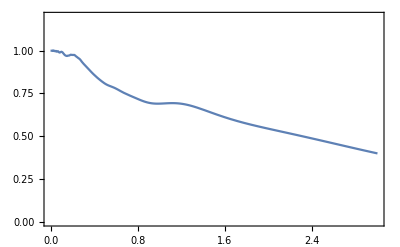

```mathematica
Plot[{FavRaw1},{b1,0.,3},PlotRange->{0,1.2},Frame->True]
```

```mathematica
data=Cases[Plot[{FavRaw1},{b1,0.0,2.5},Frame->True],Line[data_]:>data,-4,1][[1]];
Export["file5.dat",data,"Table"]
```

file5.dat

```mathematica
Plot[{FavRaw1}/.{AN->2.2,AC->0.4,n->1,m->1,k->1,l->1,q->1,p->1},{b1,0.04,0.06},PlotRange->{0,1.2},Frame->True]
```

```mathematica
FindMaximum[{FavRaw/.{AN->2.2,AC->0.4,n->1,m->2,k->2,l->2,q->2,p->2},0.049<=b1<=0.055},{b1,0.01}]
```

{0.998533,{b1→0.0500058}}

```mathematica
tg=n*π/b1/.{n->1,b1->0.05000575589845486} (*b1 in units of MHz-> tg in units of microseconds*)
```

62.8246

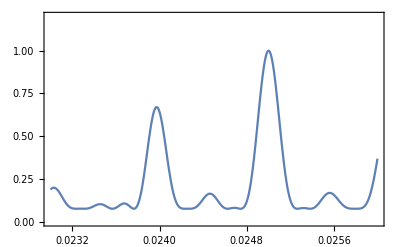

```mathematica
Plot[{FavRaw}/.{AN->2.2,AC->0.4,n->1,m->2,k->2,l->2,q->2,p->2},{b1,0.023,0.026},PlotRange->{0,1.2},Frame->True]
```

```mathematica
FindMaximum[{FavRaw/.{AN->2.2,AC->0.4,n->1,m->2,k->2,l->2,q->2,p->2},0.0246<=b1<=0.0255},{b1,0.01}]
```

{0.999631,{b1→0.0250007}}

```mathematica
tg=n*π/b1/.{n->1,b1->0.025000720799392237} (*b1 in units of MHz-> tg in units of microseconds*)
```

125.66

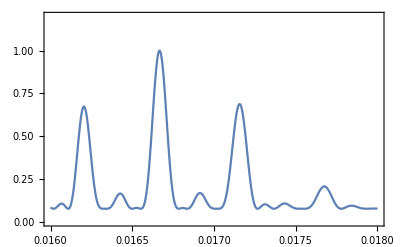

```mathematica
Plot[{FavRaw}/.{AN->2.2,AC->0.4,n->1,m->2,k->2,l->2,q->2,p->2},{b1,0.016,0.018},PlotRange->{0,1.2},Frame->True]
```

```mathematica
FindMaximum[{FavRaw/.{AN->2.2,AC->0.4,n->1,m->2,k->2,l->2,q->2,p->2},0.0165<=b1<=0.0168},{b1,0.001}]
```

{0.999836,{b1→0.0166669}}

```mathematica
tg=n*π/b1/.{n->1,b1->0.016666880304675197} (*b1 in units of MHz-> tg in units of microseconds*)
```

188.493

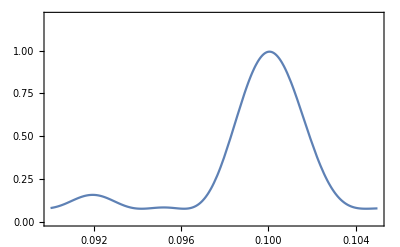

```mathematica
Plot[{FavRaw}/.{AN->2.2,AC->0.4,n->1,m->2,k->13,l->11,q->22,p->24},{b1,0.09,0.105},PlotRange->{0,1.2},Frame->True]
```

```mathematica
FindMaximum[{FavRaw/.{AN->2.2,AC->0.4,n->1,m->2,k->13,l->11,q->22,p->24},0.098<=b1<=0.102},{b1,0.001}]
```

{0.994277,{b1→0.100046}}

```mathematica
tg=n*π/b1/.{n->1,b1->0.10004572722039048} (*b1 in units of MHz-> tg in units of microseconds*)
```

31.4016

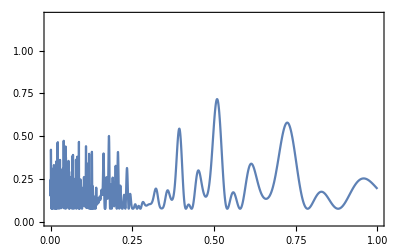

```mathematica
(*For n >1 it seems to become more difficult*)Plot[{FavRaw}/.{AN->2.2,AC->0.4,n->3,m->3,k->17,l->14,q->28,p->31},{b1,0,1},PlotRange->{0,1.2},Frame->True]
```

```mathematica
UCZ=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -ⅈ, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
FavRawCZ=(Abs[Tr[UCZ.Uc3]]^2+12)/156//FullSimplify//ComplexExpand;
```

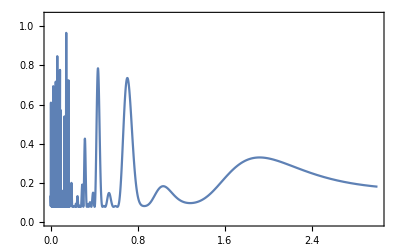

{0.990137,{b1→0.0864049}}

```mathematica
FavCZ=FavRawCZ/.{AN->2.16,AC->0.43,n->2};
Plot[{FavCZ}/.{m->5,k->30,p->55,q->50,l->25},{b1,0.0,3},PlotRange->{0.,1.05},Frame->True] 
localMax8=FindMaximum[{FavCZ/.{m->5,k->30,p->55,q->50,l->25},0.079<=b1<=0.089},{b1,0.086}]
```